# Kinetic-J numeric integration proof of concept.

Purpose: The purpose of this worksheet was to an initial investigation to check if a numeric evaluation of the velocity space and time integrals compares to the analytic result. It would also allow investigation of the phase space and temporal resolution needed for various conditions. 

Result: The testing here showed that we could indeed numerically evaluate the integrals and obtain agreement with the standard result, and that moving forward with a generalized numeric evaluator of the kinetic plasma current given some wave electric field is well posed. 

Approach: We compare the standard kinetic expressions for sigma_3,3 with numeric evaluation of the same. The numeric evaluation is done both for some limited (definite) integral range in both time and velocity (the v1, f1, and j1 quantities), and also the indefinite integrals to t=-Infinity and v=+/- Infinity (indicated by the v1Indef, f1Indef, and j1Indef quantities).

Integration Parameters: The range of the definite velocity space integrals are specified with the thisnvTh parameter, i.e., the number of vTh to integrate out to. Similarly with the time integral with the thisnRF specifying the number of RF periods to integrate back in time over. 

Update: While the sigma benchmarks now do the same thing using the actual kinetic-j code and for more cases, this sheet remains but isn’t utilized.

## Setup the standard sigma_3,3 expression.

```mathematica
wpe[n_]:=Sqrt[n q^2/(m ϵ0)];
(*wce[Z_]:=Abs[Z] q b0 /m;*)
ζ[vTh_,k_,ω_]:=ω/(k vTh);
Z[x_]:= I Sqrt[Pi] Exp[-x^2] Erfc[-I x];
(*Z[x_]:= I Sqrt[Pi] Exp[-x^2] (1+Erfi[-I x/I]/I);*)
Zp[x_]:=-2 (1+x Z[x]);
K3[vTh_,k_,ω_,n_]=FullSimplify[1-wpe[n]^2/(ω k vTh) Sum[BesselI[b,0] ζ[vTh,k,ω] Zp[ζ[vTh,k,ω]],{b,0,0}]];
sig33[vTh_,ω_,k_,n_]=Simplify[-(K3[vTh,k,ω,n]-1) I ω ϵ0];
stixP[n_]:=1-wpe[n]^2/ω^2;
sig33Cold[n_]:=-(stixP[n]-1) I ω ϵ0;
vTh[someeV_]:=Sqrt[2 someeV eCharge/m];
```

## Setup the functions for v1, f1, and j1 (both definite and indefinite).

```mathematica
x[v_,t_]:=v t+x0;
eField[v_,t_,E0_]:= E0 Exp[-I (k x[v,t]+ω t )];
v1[v_,nRF_,rfPeriod_,E0_]=Module[{t},q/m Integrate[eField[v,t,E0],{t,-nRF rfPeriod,0}]];
v1Indef[v_,E0_]=Module[{t},q/m Integrate[eField[v,t,E0],{t,-Infinity,0},Assumptions->{k∈Reals,v∈Reals,Im[ω]>0}]];
(*v1[v_,nRF_,rfPeriod_,E0_]:=-I (-1+Exp[I nRF rfPeriod (k v +ω)]) E0 q /(m (k v +ω));
v1Indef[v_,E0_]:=I E0 q/(m(k v + ω));*)
f[v_,vTh_,n_]= n/(vTh Sqrt[Pi]) Exp[-v^2/vTh^2];
f1[v_,vTh_,n_,nRF_,rfPeriod_,E0_]=-v1[v,nRF,rfPeriod,E0] D[f[v,vTh,n],v];
f1Indef[v_,vTh_,n_,E0_]=-v1Indef [v,E0]D[f[v,vTh,n],v];
j1[n_,vTh_,nRF_,rfPeriod_,E0_,nvTh_,nvPts_]:=Module[{v},q NIntegrate[ v f1[v,vTh,n,nRF,rfPeriod,E0],{v,-nvTh vTh,nvTh vTh},AccuracyGoal->3,Method->{"TrapezoidalRule","RombergQuadrature"->False}]];
j1Indef[n_,vTh_,E0_]=Module[{v},q Integrate[v f1Indef[v,vTh,n,E0],{v,-Infinity,Infinity},Assumptions->{k∈Reals,v∈Reals,Im[ω]>0,Re[ω]>0,vTh∈Reals,vTh>0,Abs[k]>0}]];
(*sig33Dlg=FullSimplify[j1Indef[n,vTh,1],Assumptions->{Im[k/ω]>0}]*)
```

## Calculate and plot the standard sigma_3,3 for some parameters

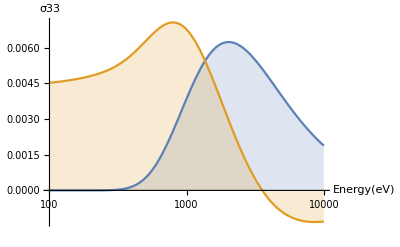

```mathematica
eCharge=1.60217646 10^-19; m=9.10938188 10^-31;
q=-eCharge;
freq=1.15 10^8;
E0=5000;
rfPeriod=1/freq;
x0=101.3;
n=1.1 10^14;
k = 22.11;
nRF =5;
ω=2 Pi freq +I 2 Pi freq 1 10^-5;
vPhs=Re[ω/k];
vGroup[n_,vTh_,k_]:=3/2 k vTh^2/wpe[n];
tPhs=0.5 m vPhs^2/eCharge;
kPer=0;
vTh[500];
vGroup[n,vTh[500],k] nRF rfPeriod 0.5;
λ=2 Pi /k;
ϵ0=8.854187817 10^-12;
vTh[500] rfPeriod nRF;

LogLinearPlot[{Re[sig33[vTh[EeV],ω,k,n]],Im[sig33[vTh[EeV],ω,k,n]]},{EeV,100,10000},Filling->Axis,AxesLabel->{Energy [eV],σ33}]
Plot[{Re[Z[x]],Im[Z[x]]},{x,-5,5},AxesLabel->{"ζ","Z(ζ)"}];
Plot[{Re[Zp[x]],Im[Zp[x]]},{x,-5,5},AxesLabel->{"ζ","Z'(ζ)"}];
ContourPlot[Abs[Z[x+I y]],{x,0,3.5},{y,-3.0,3.0},Contours->{0.1,0.2,0.3,0.4,0.5,0.7,1.0,2.0,3.0,10.0,100.0},PlotLabel->"Contour of Z(ζ) for x-axis Re(ζ), y-axis Im(ζ)"];
tValsZ={100,200,300,500,800,1000,1500,2000,3000,4000,5000,6000,7000,10000};
reValsZ= Table[{rteV,Re[sig33[vTh[rteV],ω,k,n]]},{rteV,tValsZ}];
imValsZ= Table[{rteV,Im[sig33[vTh[rteV],ω,k,n]]},{rteV,tValsZ}];
(*Export["sig33_mathematica.nc",{reValsZ,imValsZ},"NetCDF"];*)
```

## Look at the velocity space of the v0*f1 term for some temperature and integration parameters.

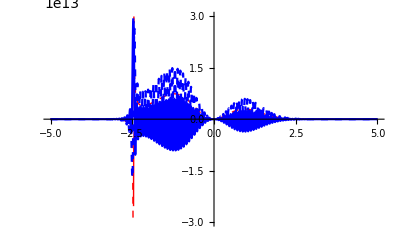

```mathematica
thiseV=500;
thisnRF=30;
thisnvTh=5;
Plot[{Re[thisv vTh[thiseV] f1Indef[thisv vTh[thiseV],vTh[thiseV],n,E0]] ,
Im[thisv vTh[thiseV] f1Indef[thisv vTh[thiseV],vTh[thiseV],n,E0]],
Re[thisv vTh[thiseV] f1[thisv vTh[thiseV],vTh[thiseV],n,thisnRF,rfPeriod,E0]],Im[thisv vTh[thiseV]f1[thisv vTh[thiseV],vTh[thiseV],n,thisnRF,rfPeriod,E0]]},{thisv,-thisnvTh ,thisnvTh},PlotStyle->{Directive[Red,Thick],Directive[Red,Dashed,Thick],Blue,Directive[Blue,Dashed]},PlotRange->0.3 10^14]
```

## Compare the definite and indefinite evaluations of j1 for a single temperature.

```mathematica
thiseV=500;
thisnRF=5;
thisnvTh=5;
thisnPts=500;
j1[n,vTh[thiseV],thisnRF,rfPeriod,E0,thisnvTh,thisnPts]
j1Indef[n,vTh[thiseV],E0]
```

4.04223-31.1678 ⅈ

4.04227-31.1677 ⅈ

These agree, so the definite integral over useful numeric ranges reproduces the  indefinite integral over infinite range.

## Compare temperature dependence of the analytic sigma_3,3 with the numerically evaluated values from j1 / E1.

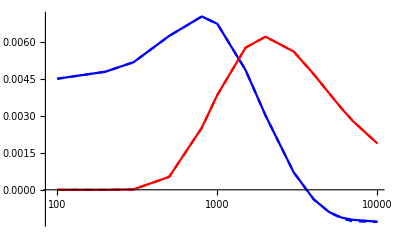

```mathematica
tVals={100,200,300,500,800,1000,1500,2000,3000,4000,5000,6000,7000,10000};
thisnRF =10;
thisnvTh = 4;
thisnPts=500;
reVals= Table[{rteV,
Re[j1[n,vTh[rteV],thisnRF,rfPeriod,E0,thisnvTh,thisnPts]/eField[0,0,E0] ]},{rteV,tVals}];
imVals=Table[{rteV,
Im[j1[n,vTh[rteV],thisnRF,rfPeriod,E0,thisnvTh,thisnPts]/eField[0,0,E0]]},{rteV,tVals}];
ListLogLinearPlot[{reVals,imVals,reValsZ,imValsZ},PlotStyle->{Red,Blue,Directive[Red,Dashed],Directive[Blue,Dashed]},Joined->True]
```

The curves here overlay well, indicating that a numeric approach should work.